What about Palindromes where the first half of the word equals the last half, both from left to right? Reduplication plus Palindromes is... ! Filtering by DictionaryWordQ (these words are all vetted, it’s okay)...

```mathematica
Reversible Palindromes, where the First Half of the Word Equals the Last Half.
```

Syntax::sntxf: "Reversible Palindromes" cannot be followed by ", where the First Half of the Word Equals the Last Half.".

Syntax::sntxi: Incomplete expression; more input is needed .

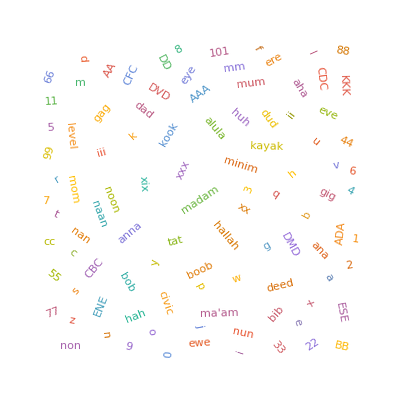

```mathematica
WoRdyLisT = Select[WordList["KnownWords"], DictionaryWordQ];
words=Select[WoRdyLisT,#==StringReverse[#]&];
WordCloud[words,WordOrientation->"Random"]
```

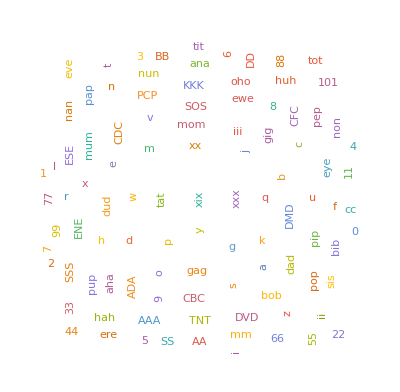

```mathematica
firstHalf[w_String]:=StringTake[w,{1,Floor[StringLength[w]/2.0]}];
lastHalf[w_String]:=StringTake[w,{-Floor[StringLength[w]/2.0],-1}];
words=Select[words,firstHalf[#]==lastHalf[#]&];
WordCloud[words,WordOrientation->"HorizontalVertical"]
```

```mathematica
Where' s Waldo: The Reduplication Requirement.
```

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
Why are yob and boy valid but not amora, in the original list?
```

Syntax::sntxf: "Why are yob and boy valid but not amora" cannot be followed by ", in the original list?".

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
notPalindromes=Select[WoRdyLIsT,#!=StringReverse[#]&];
conceptNet=NetModel["ConceptNet Numberbatch Word Vectors V17.06"];
WordBogusPair[w1_String,w2_String]:=w1<>" "<>w2->Flatten[conceptNet[{w1}]].Flatten[conceptNet[{w2}]];
PhraseBogusPair[phrase_String]:=Apply[WordBogusPair,Flatten[StringSplit[phrase," "]]]
wordPairs=Union[Drop[Map[#&,
{#,StringReverse[#], PhraseBogusPair[#<>" "<>StringReverse[#]][[2]]}&/@Select[notPalindromes,DictionaryWordQ[StringReverse[#],IgnoreCase->True]&]
],1]];
innerProduct=ToExpression /@ Select[Map[#[[3]] &,wordPairs[[2;;Length[wordPairs]]]], #>0&];
phraseBogusBound[bound_]:=Select[wordPairs,#[[3]]>bound&]
sortReversibleWords=Sort[phraseBogusBound[0.3],#1[[3]]<#2[[3]]&];
```

```mathematica
With[{length=Length[sortReversibleWords]},Grid[
Prepend[
sortReversibleWords, 
{"Word",
 "Reverse", 
"Inner Product"}],
Alignment->Left,
Spacings->{0,0},
Background->{{
{},
CMYKColor[0,0,0,0],
{}},
Table[
CMYKColor[1-(i/length),i/length,0,0,.1],
{i,1,length + 1}]}]]
```

-Graphics-

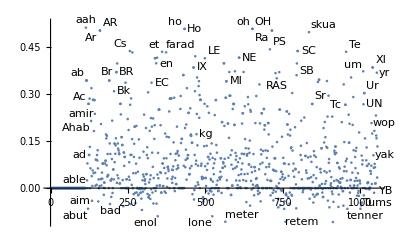

```mathematica
Show[
ListPlot[
Table[
Labeled[{i, 
wordPairs[[i]][[3]]},
wordPairs[[i]][[1]]],
{i,1,Length[wordPairs]}]],
ImageSize-> Full]
```

```mathematica
BarChart[Map[#[[3]] &, sortReversibleWords],
ChartLabels->Map[#[[1]] &, sortReversibleWords], 
ChartStyle->"Pastel",
BarSpacing->1,
ImageSize->Full,
BarOrigin->Left,
 Epilog->{Black,Thin,Line[{{0.3,0},{0.3,Length[yAxis]}}]},
FrameLabel->"Reversible Words",
Frame->True]
```

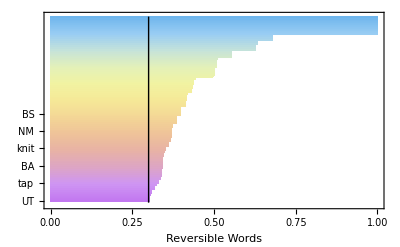

-Graphics-